### Week 8/9 Questions

#### Problem 1) Exact

```mathematica
c={{9^2+4*9*3,4*Sqrt[9*12]*0.2},{4*Sqrt[9*12]*0.2,12^2+4*12*2}}
```

{{189,8.31384},{8.31384,240}}

```mathematica
Eigenvalues[c]^0.5
```

{15.5345,13.6996}

```mathematica
Eigensystem[c]
```

{{241.321,187.679},{{0.156932,0.987609},{-0.987609,0.156932}}}

#### Problem 2) TDA Approx

```mathematica
tda={{9+2*3,0.4},{0.4,12+2*2}}
```

{{15,0.4},{0.4,16}}

```mathematica
Eigenvalues[tda]
```

{16.1403,14.8597}

% error transition frequencies

```mathematica
Abs[14.859687576256716-13.699595840607591]/13.699595840607591*100
```

8.46807

```mathematica
Abs[16.140312423743286-15.534512345226906]/15.534512345226906*100
```

3.8997

Kohn-Sham Shift errors

exact Kohn-Sham shifts

```mathematica
13.699595840607591-9.
```

4.6996

```mathematica
15.534512345226906-12.
```

3.53451

TDA Kohn-Sham shifts

```mathematica
14.859687576256716-9
```

5.85969

```mathematica
16.140312423743286-12
```

4.14031

% errors Kohn-Sham shifts

```mathematica
Abs[5.859687576256716-4.699595840607591]/4.699595840607591*100
```

24.6849

```mathematica
Abs[4.140312423743286-3.534512345226906]/3.534512345226906*100
```

17.1396

#### Problem 3) Small Matrix Approximation (SMA)

```mathematica
sma={{189,0},{0,240}}
```

{{189,0},{0,240}}

```mathematica
Sqrt[189.]
Sqrt[240.]
```

13.7477

15.4919

% Errors transition frequencies

```mathematica
(Abs[13.74772708486752-13.699595840607591])/13.699595840607591*100
```

0.351333

```mathematica
Abs[15.491933384829668-15.534512345226906]/15.534512345226906*100
```

0.274093

% Errors Kohn-Sham shifts

```mathematica
13.74772708486752-9
```

4.74773

```mathematica
15.491933384829668-12
```

3.49193

```mathematica
Abs[4.74772708486752-4.699595840607591]/4.699595840607591*100
```

1.02416

```mathematica
Abs[3.491933384829668-3.534512345226906]/3.534512345226906*100
```

1.20466

#### Problem 4) Single Pole Approx (SPA)

Sets B = 0 and ignores the off-diagonals of A. Eigenvalues are 15 and 16 eV. % error
transition frequency

```mathematica
Abs[15-13.699595840607591]/13.699595840607591*100
```

9.49228

```mathematica
Abs[16-15.534512345226906]/15.534512345226906*100
```

2.99647

% error Kohn-Sham shifts

```mathematica
Abs[6.-4.699595840607591]/4.699595840607591*100
```

27.6706

```mathematica
Abs[4-3.534512345226906]/3.534512345226906*100
```

13.1698

#### Problem 5) Calculate exact oscillator strengths

```mathematica
Eigenvectors[c]
```

{{0.156932,0.987609},{-0.987609,0.156932}}

Oscillator Strength freq 13.70 eV

```mathematica
a={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{Sqrt[9],0},{0,Sqrt[12]}}.{-0.9876094704827448,0.15693162145594639}
```

-1.08672

```mathematica
2/3*a^2
```

0.787306

Oscillator strength transition freq 15.5 eV

```mathematica
b={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{Sqrt[9],0},{0,Sqrt[12]}}.{0.15693162145594639,0.9876094704827448}
```

0.564838

```mathematica
2/3*b^2
```

0.212694

#### Problem 6) Calculate TDA oscillator strengths

```mathematica
Eigenvalues[tda]
```

{16.1403,14.8597}

```mathematica
Eigenvectors[tda]
```

{{0.331007,0.943628},{-0.943628,0.331007}}

```mathematica
tdaa1={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{16.140312423743286,0},{0,14.859687576256716}}^0.5.{0.33100694143550047,0.9436283191604177}
```

0.921725

```mathematica
2/3*tdaa1^2
```

0.566384

```mathematica
tdaa2={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{16.140312423743286,0},{0,14.859687576256716}}^0.5.{-0.9436283191604177,0.33100694143550047}
```

-1.3256

```mathematica
2/3*tdaa2^2
```

1.17148

Thomas-Reiche-Kuhn sum rule not satisfied

```mathematica
1.1714775573875067+0.5663844147889607
```

1.73786

#### Problem 7) Calculate SMA and SPA oscillator strengths

SMA oscillator strengths

```mathematica
Eigenvectors[sma]
```

{{0,1},{1,0}}

```mathematica
Eigenvalues[sma]^0.5
```

{15.4919,13.7477}

```mathematica
sma1={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{15.491933384829668,0},{0,13.74772708486752}}^0.5.{0,1}
```

0.414544

```mathematica
2/3*sma1^2
```

0.114564

```mathematica
sma2={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{15.491933384829668,0},{0,13.74772708486752}}^0.5.{1,0}
```

1.5244

```mathematica
2/3*sma2^2
```

1.54919

Thomas-Reiche-Kuhn sum rule not satisfied

```mathematica
1.549193338482967+0.11456439237389596
```

1.66376

SPA oscillator strengths

```mathematica
spa1={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{15,0},{0,16}}^0.5.{0,1}
```

0.447214

```mathematica
2/3*spa1^2
```

0.133333

```mathematica
spa2={(3.*9/10)/(2*9),(3*1/10)/(2*12)}^0.5.{{15,0},{0,16}}^0.5.{1,0}
```

1.5

```mathematica
2/3*spa2^2
```

1.5

Thomas-Reiche-Kuhn sum rule not satisfied

```mathematica
1.5+0.1333333333333333
```

1.63333

#### Problem 8) Using Lorentzians of width 0.2, plot the abs spect

```mathematica
exactspec=PDF[CauchyDistribution[15.534512345226906,0.2*0.2126943203910974],x]+PDF[CauchyDistribution[13.699595840607591,0.2*0.7873056796089029],x];
tdaspec=PDF[CauchyDistribution[16.140312423743286,0.2*0.5663844147889607],x]+PDF[CauchyDistribution[14.859687576256716,0.2*1.1714775573875067],x];
smaspec=PDF[CauchyDistribution[16.140312423743286,0.2*0.1333333333333333],x]+PDF[CauchyDistribution[14.859687576256716,0.2*1.5],x];
ksspec=PDF[CauchyDistribution[9,0.2*9/10],x]+PDF[CauchyDistribution[12,0.2*1/10],x];
```

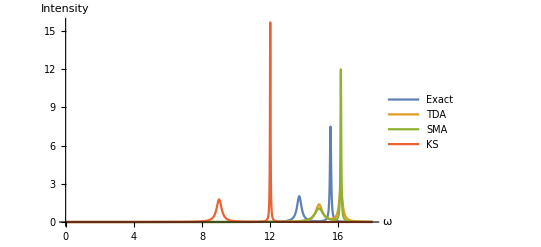

```mathematica
p1=Plot[{exactspec,tdaspec,smaspec,ksspec},{x,0,18},PlotRange->All,PlotLegends->{"Exact","TDA","SMA","KS"},AxesLabel->{"ω","Intensity"},TicksStyle->Medium,AxesStyle->Medium]
```

```mathematica
Export["spec.png",p1]
```

spec.png